# Dipole Distortion/Boost Factor TT

## Directory

```mathematica
(* Set directory to notebook's directory *)
```

```mathematica
directory=NotebookDirectory[]<>"data/"
SetDirectory[directory];
```

/home/pedro/seagate_4tb/pcloud/cmb_boost_codes_legacy/dipole_distortion/dd_effective_values/data/

```mathematica
starttime=AbsoluteTime[];
```

## Set simulation/data parameters

```mathematica
lmax=2498;
```

```mathematica
nside=2048;
```

```mathematica
gaussianbeam=5; (*In grads*)
```

```mathematica
numberofsimulations=1;
```

```mathematica
pixelwindowcorrection=1; (* 1 if you want pixel window correction, 0 if don't want*)
```

```mathematica
gaussianbeamcorrection=1; (* 1 if you want pixel window correction, 0 if don't want*)
```

```mathematica
i=1; (*Dynamic counter initialization*)
```

```mathematica
fracsky=0.72514804242293485;
```

```mathematica
T0=2.7255 10^6;
```

```mathematica
lmin=3;
```

```mathematica
llim=2002;
```

```mathematica
βfid2018=0.00123357;
```

```mathematica
nthread=8;
```

```mathematica
LaunchKernels[nthread]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
freqs={30,44,70,100,143,217,353,545,857};
(*freqs={30,44,70,100.9,142.87,221.15,357.5,555.2,866.8};*)
freqshigh=freqs[[4;;]];
```

## Channels and dipole Doppler Factors by channel

```mathematica
freqs={30,44,70,100,143,217,353,545,857};
(*freqs={30,44,70,100.9,142.87,221.15,357.5,555.2,866.8};*)
freqshigh=freqs[[4;;]];
```

```mathematica
Q[ν_]:=(ν/(2*(56.79)))*Coth[(ν/(2*(56.79)))]
boostfactors=2*Q/@freqs
boostfactorshigh=boostfactors[[4;;]];
```

{2.0463,2.09906,2.24703,2.4919,2.95964,3.99224,6.24076,9.59806,15.0907}

## SMICA weights

#### Importing Weights

```mathematica
weightsFULL2013=Import["weights_T_smica_R1.00.txt","Table"];
```

```mathematica
weightsFULL2018=Import["weights_T_smica_R3.00_Xfull.txt","Table"];
```

```mathematica
weightsHIGH2018=Import["weights_T_smica_R3.00_Xhigh.txt","Table"];
```

```mathematica
beamcorrection=Table[Import["ibl"<>ToString[freqs[[freq]]]<>"_T.fits","TableData"],{freq,Dimensions[freqs][[1]]}][[All,1]]
```

{{{1.01049},{1.01049},{1.01049},{1.00935},{1.0073},{1.00831},{1.01022},{1.01016},{1.0091},{1.00928},{1.0105},{1.01073},{1.01003},3975,{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.}},7,{1}}
 |  |  |  |

```mathematica
beamcorrection=Table[beamcorrection[[freq]][[All,1]],{freq,Dimensions[freqs][[1]]}]
```

{{1.01049,1.01049,1.01049,1.00935,1.0073,1.00831,1.01022,1.01016,1.0091,1.00928,1.0105,1.01073,1.01003,1.00997,1.01089,3971,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},7,{1}}
 |  |  |  |

#### Maps conversions

```mathematica
c=0.017606;
corr[x_]:=(Exp[c x]-1)^2/((c x)^2 Exp[c x])
```

```mathematica
toKrj=corr/@freqs
toKrjhigh=toKrj[[4;;]];
```

{1.02347,1.05102,1.13316,1.28653,1.65339,2.99043,12.8972,159.588,15685.6}

```mathematica
toKcmb={0.977074,0.951459,0.882496,0.7776114060000001,0.6048402900000001,0.334590078,0.0775485398,0.00635955563,0.00010051383700000001};
toKcmbhigh=toKcmb[[4;;]];
```

```mathematica
toKcmb/(1/toKrj)
```

{1.,1.,1.00001,1.00042,1.00004,1.00057,1.00016,1.01491,1.57662}

```mathematica
MjyToKcmb={1,1,1,1,1,1,1,58.0356,2.2681};
MjyToKcmbhigh=MjyToKcmb[[4;;]];
```

```mathematica
weightsFULLCMB2013=((weightsFULL2013*toKrj));
```

```mathematica
weightsFULLCMB2018=((weightsFULL2018)/(toKcmb));
```

```mathematica
weightsHIGHCMB2018=((weightsHIGH2018)/(toKcmbhigh));
```

```mathematica
wMjyKcmbFULL2018=weightsFULL2018/MjyToKcmb;
wMjyKcmbHIGH2018=weightsHIGH2018/MjyToKcmbhigh;
```

#### SMICA Weights Plots

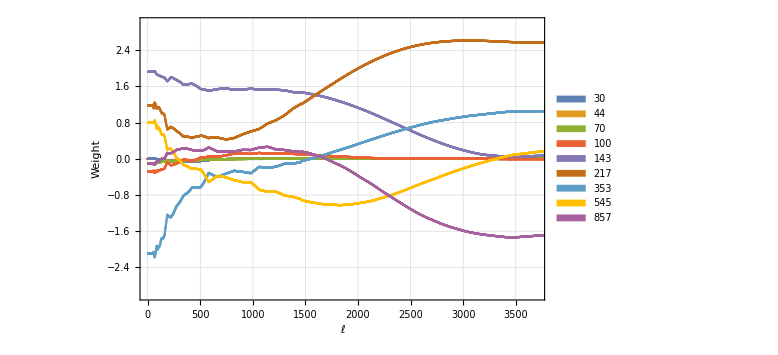

```mathematica
ListPlot[weightsFULLCMB2013,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],PlotRange->{{1,3700},{-3,3}},ImageSize-> Large,FrameLabel->{Style["ℓ",17],"Weight",Style["SMICA FULL 2013",17]}]
```

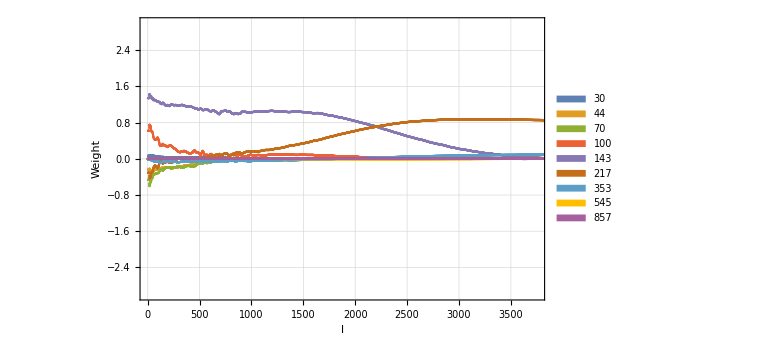

```mathematica
ListPlot[weightsFULL2018,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],PlotRange->{{1,3750},{-3,3}},ImageSize-> Large,FrameLabel->{"l","Weight",Style["SMICA FULL 2018",15]}]
```

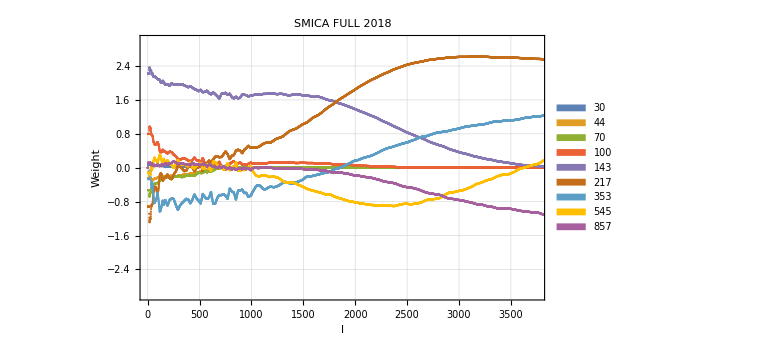

```mathematica
weightsFULLCMB2018plot=ListPlot[weightsFULLCMB2018,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],PlotRange->{{1,3750},{-3,3}},ImageSize-> Large,FrameLabel->{Style["l",17],Style["Weight",17]},PlotLabel->Style["SMICA FULL 2018",17],FrameTicksStyle->Directive[Thick,12]]
```

```mathematica
Export["weightsFULLCMB2018plot.pdf",weightsFULLCMB2018plot]
```

weightsFULLCMB2018plot.pdf

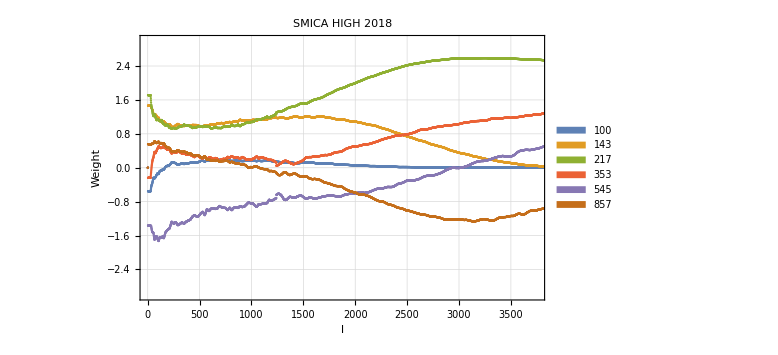

```mathematica
ListPlot[weightsHIGHCMB2018,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqshigh],PlotRange->{{1,3750},{-3,3}},ImageSize->Large,FrameLabel->{Style[#,17]&@"l",Style[#,17]&@"Weight"},PlotLabel->Style["SMICA HIGH 2018",17]]
```

#### SMICA 2018 Pipeline

```mathematica
HighPassCos[l_,l1_,l2_]:=Piecewise[{{0,l<l1},{1,l>l2},{0.5*(1-Cos[π*((l-l1)/(l2-l1))]),l1 ≤ l≤ l2}}]
```

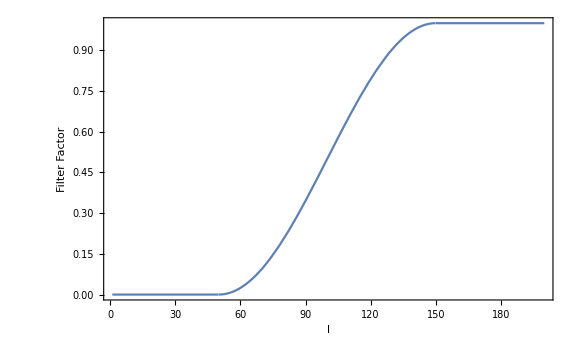

```mathematica
HighPassCosplot=Plot[HighPassCos[l,50,150],{l,1,200},Frame->True,FrameLabel->{Style["l",17],Style["Filter Factor",17],Style["HighPass Filter",15]},ImageSize->Large]
```

```mathematica
Export["HighPassCosplot.pdf",HighPassCosplot]
```

HighPassCosplot.pdf

```mathematica
transitionMASKweight=0.7; (*Subscript[Fsky, TransitionMask*UT79symmmask]/Subscript[Fsky, UT79symmmask] 0.939790295308*)
```

```mathematica
beamtab=Table[Table[beamcorrection[[freq,l]],{freq,1,9}],{l,1,4001}];
beamtabhigh=Table[Table[beamcorrection[[freq,l]],{freq,4,9}],{l,1,4001}];
```

```mathematica
P[l_]:=transitionMASKweight*HighPassCos[l,50,150]
Subscript[Xnotcorr, Full][l_]:=(weightsFULL2018[[All,l]]/beamtab[[l]])/{0.98961854,0.99757886,0.99113965,1,1,1,1,1,1};
Subscript[Xnotcorr, High][l_]:=weightsHIGH2018[[All,l]]/beamtabhigh[[l]];
Xnotcorr[l_]:=Subscript[Xnotcorr, Full][l]+P[l]*(Flatten[Append[{0,0,0},Subscript[Xnotcorr, High][l]]]-Subscript[Xnotcorr, Full][l]) (* X = Subscript[X, Full] + P(Subscript[X, High]-Subscript[X, Full]) *)
```

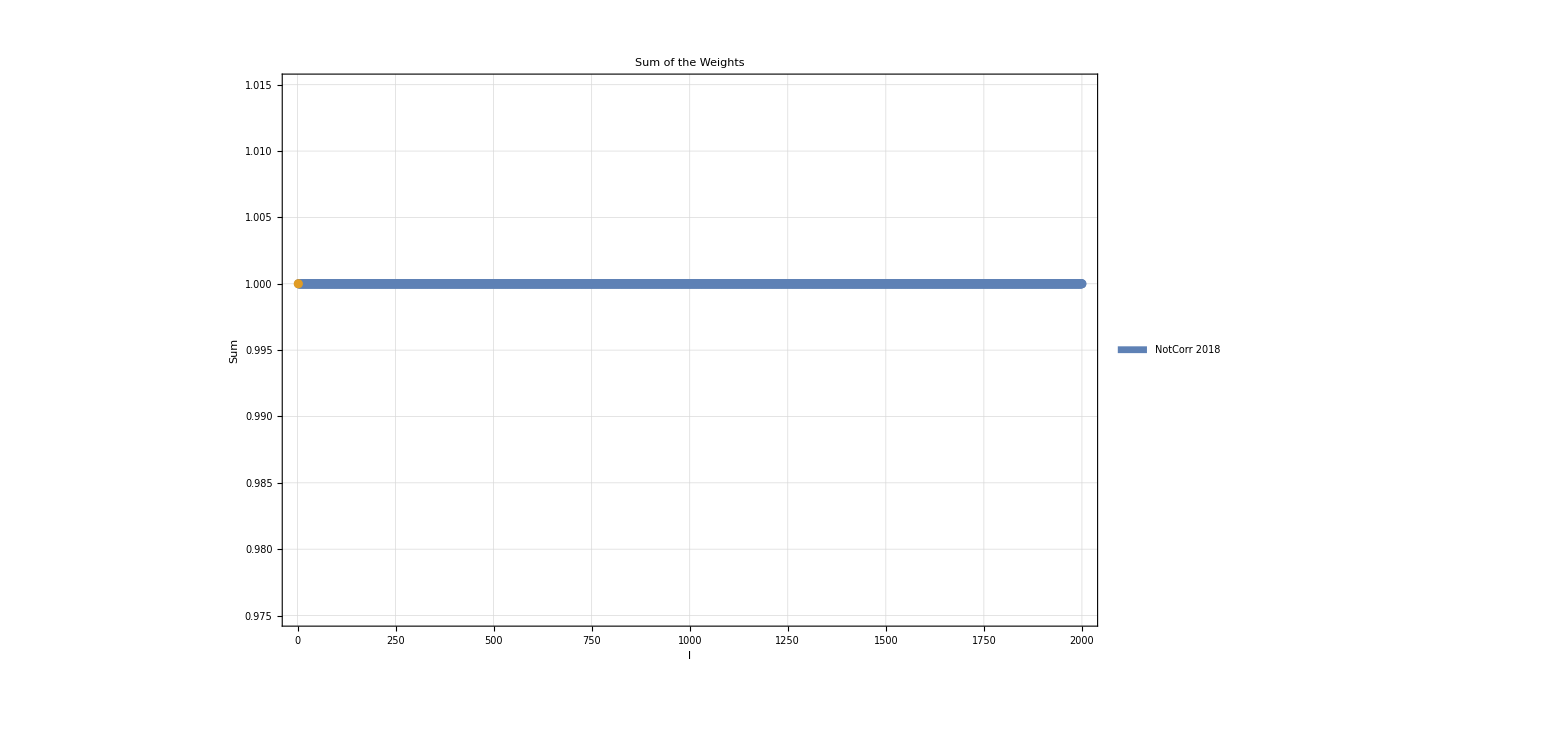

```mathematica
plot=ListPlot[{Table[Total[Xnotcorr[l]],{l,1,2000}],{l,1,2000}},GridLines->Automatic,PlotRange->{{1,2000},{0.975,1.015}},PlotLegends->Placed[SwatchLegend[{"NotCorr 2018"}],{Left,Bottom}],ImageSize->1200,Frame->True,PlotLabel->"Sum of the Weights",FrameLabel->{"l","Sum"}]
```

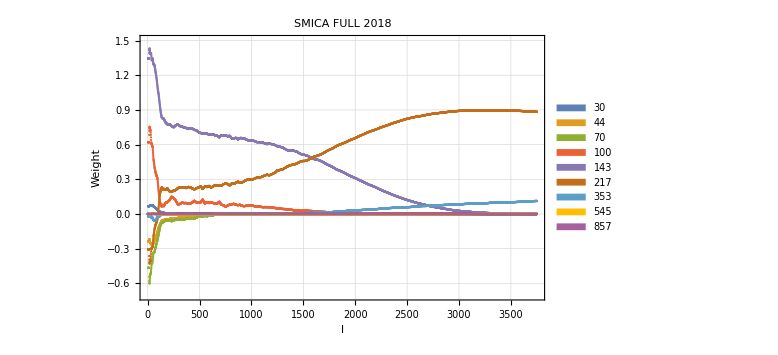

```mathematica
weightsFULLCMB2018plot=ListPlot[Table[Table[Xnotcorr[l+1],{l,0,3750}][[All,n]],{n,1,9}],PlotRange->{{1,3750},{-0.7,1.5}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],ImageSize-> Large,FrameLabel->{Style["l",17],Style["Weight",17]},PlotLabel->Style["SMICA FULL 2018",17],FrameTicksStyle->Directive[Thick,12]]
```

```mathematica
Export["weightsFULLCMB2018plot.pdf",weightsFULLCMB2018plot]
```

weightsFULLCMB2018plot.pdf

#### Effective Boost factor

```mathematica
SmicaBoostFactor2018[l_]:=-2+Total[(Xnotcorr[l]*boostfactors)]
```

```mathematica
smicatable=Table[SmicaBoostFactor2018[l],{l,10,2000}];
```

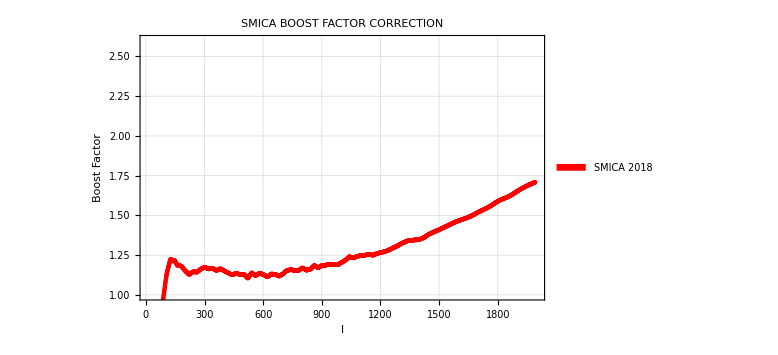

```mathematica
ListPlot[{smicatable},PlotRange->{{10,2000},{1,2.6}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018"}],PlotStyle->Red,ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

#### Binned Boost factor

```mathematica
binsize=200; nbins=10;
```

```mathematica
smicaboostfactorsbins=Table[Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}],{bin,1,nbins}]
```

{1.09257,1.15694,1.13052,1.13867,1.17993,1.24082,1.31124,1.40615,1.51744,1.64736}

```mathematica
smicaboostfactorsbinsforplot=Table[{bin*200-100,Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]
```

{{100,1.09257},{300,1.15694},{500,1.13052},{700,1.13867},{900,1.17993},{1100,1.24082},{1300,1.31124},{1500,1.40615},{1700,1.51744},{1900,1.64736}}

```mathematica
βfid2018
```

0.00123357

```mathematica
smicaboostfactorsBetaDeboostbins=smicaboostfactorsbins*βfid2018
```

{0.00134776,0.00142717,0.00139458,0.00140463,0.00145552,0.00153064,0.00161751,0.00173459,0.00187187,0.00203214}

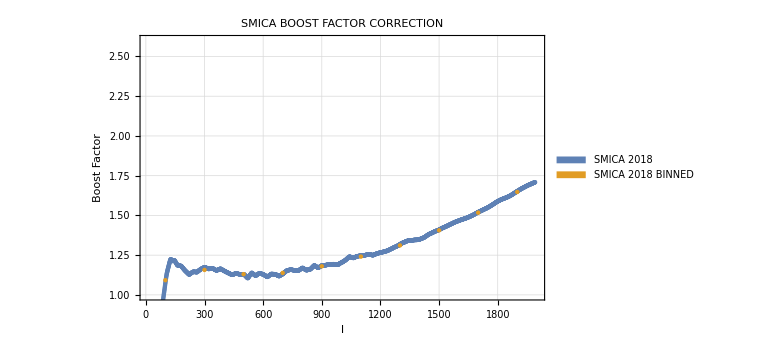

```mathematica
ListPlot[{smicatable,Table[{(binsize/2)+binsize*(bin-1),Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]},PlotRange->{{10,2000},{1,2.6}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018","SMICA 2018 BINNED"}],ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

#### Binning Expected Error

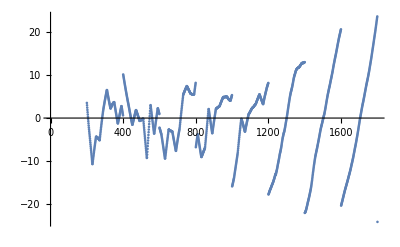

```mathematica
ListPlot[Table[{l,(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])*βfid2018*299792},{l,200,1800}]]
```

```mathematica
SmicaBinnedError=Total[Table[(2*l+1)(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]]),{l,200,1800}]*βfid2018*299792]/Total[Table[(2*l+1),{l,200,1800}]]
```

-0.165273

```mathematica
SmicaBinnedAbsError=Total[Table[(2*l+1)Abs[(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])],{l,200,1800}]*370]/Total[Table[(2*l+1),{l,200,1800}]]
```

7.84321

#### Mean Boost Factor and error

```mathematica
smicameanboostfactor=Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1,2000}]/Sum[(2l+1),{l,1,2000}]
```

1.3768

```mathematica
smicameanboostfactor200to1800=Sum[SmicaBoostFactor2018[l]*(2l+1),{l,200,1800}]/Sum[(2l+1),{l,200,1800}]
```

1.31614

```mathematica
SmicaBinnedAbsError/(smicameanboostfactor200to1800*βfid2018*299792)
```

0.0161141

```mathematica
smicaboostfactorsBetaDeboostMean=-smicameanboostfactor*βfid2018
```

-0.00169838

## NILC weights

#### Needlets definitions

```mathematica
lpeakN={0,100,200,300,400,600,800,1000,1400,1800,2200,2800,3400};
lminN={1,0,100,200,300,400,600,800,1000,1400,1800,2200,2800};
lmaxN={100,200,300,400,600,800,1000,1400,1800,2200,2800,3400,4000};
needlet[band_,l_]:=Piecewise[{{0,l<lminN[[band]]},{Cos[((lpeakN[[band]]-l)/(lpeakN[[band]]-lminN[[band]]))*π/2],lminN[[band]]≤ l<lpeakN[[band]]},{1,l==lpeakN[[band]]},{Cos[((l-lpeakN[[band]])/(lmaxN[[band]]-lpeakN[[band]]))*π/2],lpeakN[[band]]<l≤ lmaxN[[band]]},{0,l>lmaxN[[band]]}}]
```

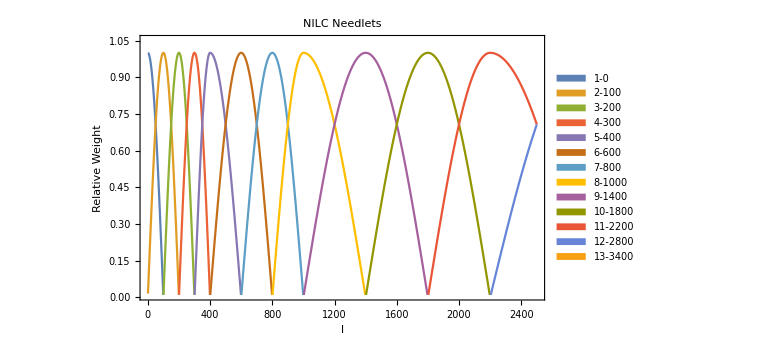

```mathematica
nilcneedletsplot=ListPlot[Table[needlet[band,l],{band,1,13},{l,1,2500}],PlotRange->{{0,2500},{0.01,1.05}},ImageSize->Large,Frame->True,FrameLabel->{Style["l",17],Style["Relative Weight",17]},PlotLabel->Style["NILC Needlets",17],PlotLegends->Placed[SwatchLegend[{"1-0","2-100","3-200","4-300","5-400","6-600","7-800","8-1000","9-1400","10-1800","11-2200","12-2800","13-3400"}],{Right,Bottom}],FrameTicksStyle->Directive[Black,15],Joined->True]
```

```mathematica
Export["nilcneedletsplot.pdf",nilcneedletsplot]
```

nilcneedletsplot.pdf

#### Band Weights

```mathematica
bandweights[band_]:=Import["isky_dx11_mean_weight.fits","Data"][[1]][[band]]
```

```mathematica
bandweightsforplot[band_]:={{0.05245975139666451,-0.10958004675020472,-0.8039010351197148,0.6790616297074396,1.5706717951544056,-0.3820284448762801,-0.004936046047593265,-0.0017633292118776507,0.000015725747304380672},{0.0219176120835205,-0.035360422884078355,-0.6767579448093127,0.5089057855241852,1.4352560583678737,-0.20930603019008864,-0.04486786195073012,0.00020387274037656996,8.931118201660209*^-6},{0.015657101798892303,-0.03807384945538229,-0.47786133368208256,0.22722544222202035,1.3442265548011625,0.024963126705395234,-0.09914809637758559,0.003014138442777073,-3.084455264478678*^-6},{0.01197718684786129,-0.025305825754428735,-0.3038895709758875,-0.0668890968525102,1.26926994645998,0.27033313981255597,-0.16205510952789673,0.006580921805155456,-0.000021591814746228383},{0.0052547371551185116,-0.01671801011845028,-0.11175341809108817,-0.2238067329847547,1.096703666706359,0.3654645729108565,-0.11804706051806485,0.002913899868818796,-0.000011654928584534907},{Null,-0.0028394226968456774,-0.0563064578064184,-0.18127825877029524,0.9604102702902025,0.3586084528668998,-0.07877418250302445,0.000181136545060592,-1.5379254049384259*^-6},{Null,Null,-0.0272427089937796,-0.1501935899230357,0.8468181486608407,0.3935714205894567,-0.0626273699336396,-0.0003153742222582688,-0.00001052617739186663},{Null,Null,-0.006198189378072794,-0.06828377297695551,0.6948064410924712,0.41675059566374456,-0.034769811863051926,-0.0022976647246368553,-7.59781275369342*^-6},{Null,Null,-0.0005703985356269886,-0.014083893557538162,0.5685401139285239,0.4636753630323638,-0.01418893290070787,-0.0033575471719367446,-0.000014704795166569695},{Null,Null,Null,-0.003180396453846355,0.41756353745633784,0.5868006547800835,0.002711654087339931,-0.003860895101886216,-0.00003455476766954071},{Null,Null,Null,-0.0006055455390523623,0.20357227383990806,0.774106470437439,0.026884017061777787,-0.003881603927339729,-0.00007561187328567391},{Null,Null,Null,Null,0.038917773047899035,0.905231421848436,0.05856785516520732,-0.0025828605053072862,-0.00013418955671655938},{Null,Null,Null,Null,0.000984437047023338,0.9119181941874867,0.08726981410333419,6.839891886337699*^-6,-0.00017928522985184866}}⟦band⟧;
```

```mathematica
colors={(*RGBColor[N[Normalize[{56,0,71}]]]*)Black,RGBColor[N[Normalize[{61,0,162}]]],RGBColor[N[Normalize[{13,0,255}]]],RGBColor[N[Normalize[{9,59,255}]]],RGBColor[N[Normalize[{25,174,255}]]],RGBColor[N[Normalize[{34,255,207}]]],RGBColor[N[Normalize[{35,255,96}]]],RGBColor[N[Normalize[{36,255,22}]]],RGBColor[N[Normalize[{86,255,13}]]],RGBColor[N[Normalize[{180,255,10}]]],RGBColor[N[Normalize[{254,211,11}]]],RGBColor[N[Normalize[{252,89,10}]]],RGBColor[N[Normalize[{251,19,29}]]]}
```

{GrayLevel[0],RGBColor[{0.35238928461181596, 0., 0.9358535099526916}],RGBColor[{0.05091427198434202, 0., 0.9987030273851704}],RGBColor[{0.034365416027046736, 0.22528439395508418, 0.9736867874329909}],RGBColor[{0.08071826920974581, 0.5617991536998309, 0.8233263459394073}],RGBColor[{0.10296886152666716, 0.7722664614500035, 0.6268986569417677}],RGBColor[{0.12740673275735537, 0.9282490529464463, 0.34945846699160327}],RGBColor[{0.13928296926770817, 0.9865876989795995, 0.08511737010804388}],RGBColor[{0.3191979202657341, 0.946458949625142, 0.04825084841226214}],RGBColor[{0.5763874626060793, 0.8165489053586124, 0.03202152570033774}],RGBColor[{0.7687868243279092, 0.6386378737527121, 0.03329391758900395}],RGBColor[{0.9422618492330557, 0.33278295468945224, 0.037391343223533956}],RGBColor[{0.9905948381758088, 0.07498526663482218, 0.11445119644262333}]}

#### Band weights plot

```mathematica
bandsWplot1=ListLogLinearPlot[Table[{freqs[[freq]],bandweightsforplot[band][[freq]]},{band,1,13},{freq,1,9}],PlotRange->{{25,1000},{-1,2.0}},(*PlotStyle->Table[{colors[[n]],PointSize[0.02]},{n,1,13}],*)Frame->True,FrameLabel->{Style["Frequency (Ghz)",17],Style["Mean Weight",17]},PlotLabel->Style["Band Weights",17],FrameTicksStyle->Directive[Black,15]];
```

```mathematica
bandsWplot2=ListLogLinearPlot[Table[{freqs[[freq]],bandweightsforplot[band][[freq]]},{band,1,13},{freq,1,9}],Joined->True,PlotRange->{{25,1000},{-1,2.0}},(*PlotStyle->Table[{colors[[n]]},{n,1,13}],*)PlotLegends->Placed[SwatchLegend[{"1","2","3","4","5","6","7","8","9","10","11","12","13"},LegendLabel->"Band (Needlet)"],{Left,Top}],Frame->True,FrameLabel->{Style["Frequency (Ghz)",17],Style["Mean Weight",17]},PlotLabel->Style["Band Weights",17],FrameTicksStyle->Directive[Black,15]];
```

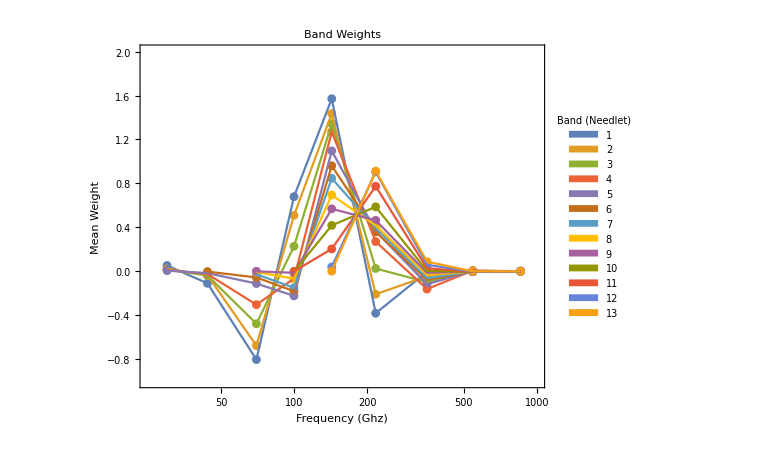

```mathematica
nilcbandsplot=Show[bandsWplot1,bandsWplot2,ImageSize-> Large,AspectRatio-> 0.8]
```

```mathematica
Export["nilcbandsplot.pdf",nilcbandsplot]
```

nilcbandsplot.pdf

#### Effective Boost Factor

```mathematica
needletWeights[band_,l_]:=bandweights[band]*needlet[band,l]
```

```mathematica
NILCweights=ParallelTable[(Total[Table[needletWeights[band,l],{band,1,13}]]/Total[Table[needlet[band,l],{band,1,13}]]),{l,1,2500}];
```

```mathematica
needlet[1,599]
```

0

```mathematica
NILCweights
```

{{0.0519874,-0.108432,-0.801935,0.67643,1.56858,-0.379357,-0.00555364,-0.0017329,0.0000156207},2498,{0.,0.,0.,-0.000302773,0.121245,0.839669,0.0427259,-0.00323223,-0.000104901}}
 |  |  |  |

```mathematica
NILCboostfactors2018[l_]:=-2+Total[NILCweights[[l]]*boostfactors]
```

```mathematica
nilcboostable=Table[NILCboostfactors2018[l],{l,1,2500}];
```

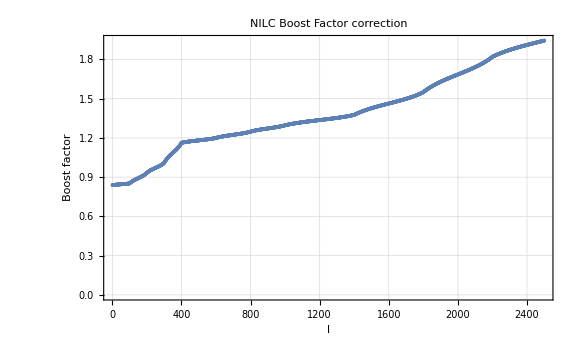

```mathematica
ListPlot[nilcboostable,GridLines->Automatic,Frame->True,PlotLabel->Style["NILC Boost Factor correction",15],FrameLabel->{"l","Boost factor"},ImageSize->Large]
```

#### Binned Boost factor

```mathematica
binsize=200; nbins=10;
```

```mathematica
nilcboostfactorsbins=Table[Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}],{bin,1,nbins}]
```

{0.884574,1.04152,1.18262,1.22516,1.27339,1.31979,1.35479,1.42602,1.50247,1.62706}

```mathematica
nilcboostfactorsbinsforplot=Table[{bin*binsize-100,Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]
```

{{100,0.884574},{300,1.04152},{500,1.18262},{700,1.22516},{900,1.27339},{1100,1.31979},{1300,1.35479},{1500,1.42602},{1700,1.50247},{1900,1.62706}}

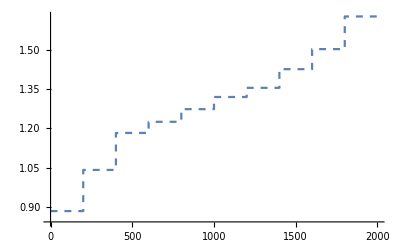

```mathematica
ListStepPlot[nilcboostfactorsbinsforplot,Center,PlotStyle->Dashed]
```

```mathematica
nilcboostfactorsBetaDeboostbins=nilcboostfactorsbins*βfid2018
```

{0.00109118,0.00128478,0.00145884,0.00151132,0.00157082,0.00162806,0.00167122,0.00175909,0.00185341,0.0020071}

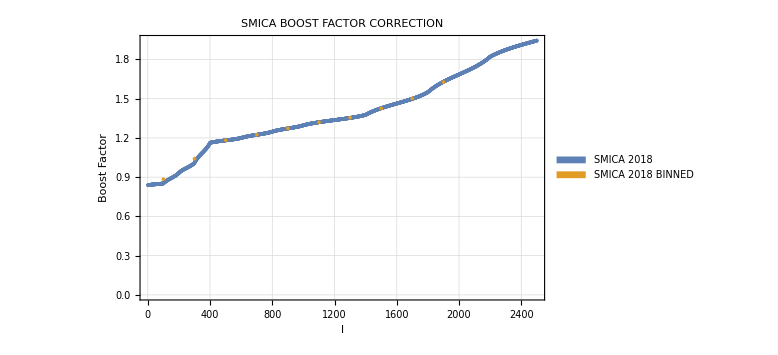

```mathematica
ListPlot[{nilcboostable,Table[{(binsize/2)+binsize*(bin-1),Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018","SMICA 2018 BINNED"}],ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

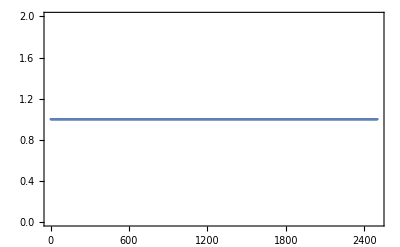

```mathematica
ListPlot[Total[NILCweights,{2}],Frame->True]
```

#### Binning Expected Error

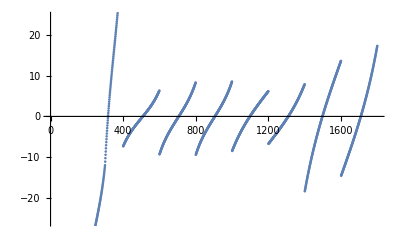

```mathematica
ListPlot[Table[{l,(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])*βfid2018*299792},{l,200,1800}]]
```

```mathematica
NilcBinnedError=Total[Table[(2*l+1)(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]]),{l,200,1800}]*βfid2018*299792]/Total[Table[(2*l+1),{l,200,1800}]]
```

-0.156384

```mathematica
NilcBinnedAbsError=Total[Table[(2*l+1)Abs[(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])],{l,200,1800}]*370]/Total[Table[(2*l+1),{l,200,1800}]]
```

5.96035

#### Mean Boost Factor and error

```mathematica
nilcmeanboostfactor=Sum[NILCboostfactors2018[l]*(2l+1),{l,1,2000}]/Sum[(2l+1),{l,1,2000}]
```

1.39924

```mathematica
nilcboostfactorsBetaDeboostMean=nilcmeanboostfactor*βfid2018
```

0.00172606

```mathematica
nilcmeanboostfactor200to1800=Sum[NILCboostfactors2018[l]*(2l+1),{l,200,1800}]/Sum[(2l+1),{l,200,1800}]
```

1.35159

```mathematica
NilcBinnedAbsError/(nilcmeanboostfactor200to1800*βfid2018*299792)
```

0.0119245

# Comparision plot TT

### Preamble

```mathematica
ckmsNU=299792;
rescaled[ddfactor_]:=IntegerPart[ddfactor*βfid2018*ckmsNU];
newaxis=Table[{rescaled[ddfactor],ddfactor},{ddfactor,0.3,2,0.1}]
```

{{110,0.3},{147,0.4},{184,0.5},{221,0.6},{258,0.7},{295,0.8},{332,0.9},{369,1.},{406,1.1},{443,1.2},{480,1.3},{517,1.4},{554,1.5},{591,1.6},{628,1.7},{665,1.8},{702,1.9},{739,2.}}

```mathematica
(*boostfactorplot=ListPlot[{smicatable,nilcboostable},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{{Style["Dipole Distortion Factor",17],Style["Effective Doppler Mod. (km/s)",17]},{Style["l",17],Style["Dipole Distortion Comparision",17]}},PlotStyle->{Red,Blue},PlotLegends->Placed[SwatchLegend[{Style[#,17]&@"SMICA",Style[#,17]&@"NILC"}],{Right,Bottom}],PlotRange->{{0,2000},{0.65,1.75}},ImageSize->Large,FrameTicks->{{Automatic,Table[{l,rescaled[l]},{l,0.6,1.8,0.2}]},{Automatic,None}},FrameTicksStyle->Directive[Thick,12],Joined->True]*)
```

```mathematica
(*Export["boostfactorplot.pdf",boostfactorplot]*)
```

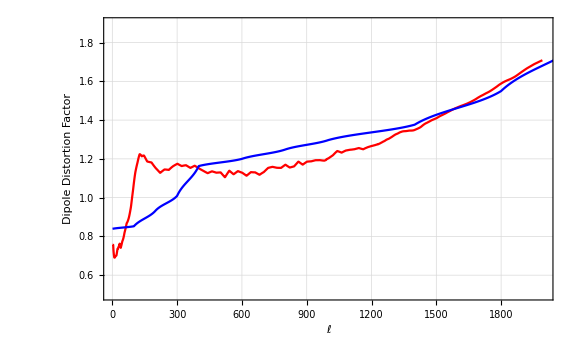

```mathematica
boostfactorplot=ListPlot[{smicatable,nilcboostable},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{{Style["Dipole Distortion Factor",28],Style["Effective Doppler Mod. (km/s)",28]},{Style[ToExpression["$\ell$",TeXForm,HoldForm],Large],""}},(*PlotLegends->Placed[SwatchLegend[{Style[#,19]&@"SMICA",Style[#,19]&@"NILC"},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&)],{Right,Bottom}],*)PlotStyle->{Red,Blue},PlotRange->{{0,2000},{0.5,1.9}},ImageSize->Large,FrameTicks->{{Automatic,Table[{l,rescaled[l]},{l,0.6,1.8,0.2}]},{Automatic,None}},FrameTicksStyle->Directive[Thick,25],PlotStyle->{{Blue,Thick},{Orange,Thick}},Joined->True]
```

```mathematica
nilcboostfactorsbinsforplot
```

{{100,0.884574},{300,1.04152},{500,1.18262},{700,1.22516},{900,1.27339},{1100,1.31979},{1300,1.35479},{1500,1.42602},{1700,1.50247},{1900,1.62706}}

```mathematica
nilcboostfactorsbinsforplot[[2-1;;2+1]]
```

{{100,0.884574},{300,1.04152},{500,1.18262}}

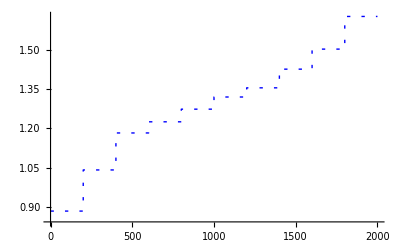

```mathematica
binnedplotnilc=ListStepPlot[nilcboostfactorsbinsforplot,Center,PlotStyle->Directive[Blue,Dashing[{0.006,0.02}],Thick],Joined->True]
```

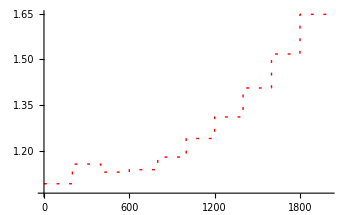

```mathematica
binnedplotsmica=ListStepPlot[smicaboostfactorsbinsforplot,Center,PlotStyle->Directive[Red,Dashing[{0.006,0.02}],Thick],Joined->True]
```

```mathematica
nilcbetameanvecnorm=Import["nilc_beta_mean_vecnorm_1024.dat","Table"];
smicabetameanvecnorm=Import["smica_beta_mean_vecnorm_1024.dat","Table"];
```

```mathematica
expectederrorbybin=Import["expected_error_by_bin_1024.dat","Table"][[All,1]];
```

```mathematica
nilcbetameannorm=Table[{117+200*(bin-1),Around[Norm[Transpose[nilcbetameanvecnorm][[bin]]]/(ckmsNU*βfid2018),(expectederrorbybin[[bin]]/Sqrt[512])/(ckmsNU*βfid2018)]},{bin,1,10}];
smicabetameannorm=Table[{83+200*(bin-1),Around[Norm[Transpose[smicabetameanvecnorm][[bin]]]/(ckmsNU*βfid2018),((expectederrorbybin[[bin]]/Sqrt[512])/(ckmsNU*βfid2018))]},{bin,1,10}];
```

```mathematica
Transpose[nilcbetameanvecnorm][[6]]
```

{-36.7839251836681456,-316.733834255655552,348.919600671331693}

```mathematica
nilcbetameannorm=Table[{117+200*(bin-1),Around[Norm[Transpose[nilcbetameanvecnorm][[bin]]]/(ckmsNU*βfid2018),(expectederrorbybin[[bin]]/Sqrt[512])/(ckmsNU*βfid2018)]},{bin,1,10}];
smicabetameannorm=Table[{83+200*(bin-1),Around[Norm[Transpose[smicabetameanvecnorm][[bin]]]/(ckmsNU*βfid2018),((expectederrorbybin[[bin]]/Sqrt[512])/(ckmsNU*βfid2018))]},{bin,1,10}];
```

```mathematica
expectederrorbybin[[4]]/Sqrt[512]
```

30.5892351442105134

```mathematica
smicabetameannorm
```

{{83,0.830.22},{283,1.150.13},{483,1.180.10},{683,1.090.08},{883,1.200.07},{1083,1.200.07},{1283,1.250.06},{1483,1.400.06},{1683,1.510.05},{1883,1.680.05}}

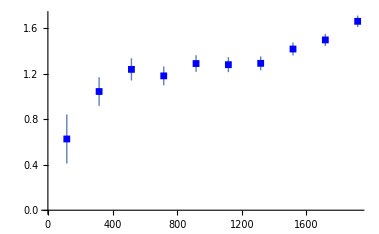

```mathematica
nilcbetameansimsplot=ListPlot[nilcbetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Blue,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

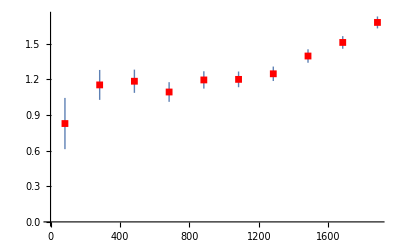

```mathematica
smicabetameansimsplot=ListPlot[smicabetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Red,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

```mathematica
(*insettitleTT=Graphics[Text[Style["TT",42],{0.5,0.6},{-2.6,-12.15}]];;*)(*para joined*)
```

### Final Plot

```mathematica
insettitleTT=Graphics[Text[Style["TT",42],{0.5,0.6},{-3,-13.9}]];
```

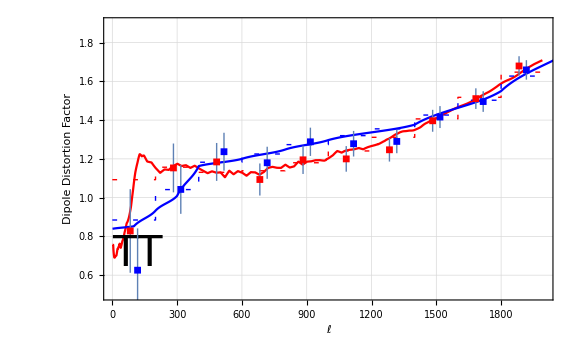

```mathematica
boostfactorplotTT=Show[{boostfactorplot,binnedplotnilc,binnedplotsmica,smicabetameansimsplot,nilcbetameansimsplot,insettitleTT}]
```

```mathematica
Export["dipole_doppler_joined_plot_1024.pdf",boostfactorplotTT]
```

dipole_doppler_joined_plot_1024.pdf

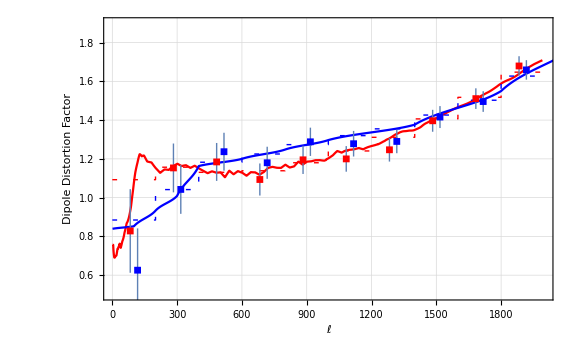

```mathematica
boostfactorplot2=Show[boostfactorplot,binnedplotnilc,binnedplotsmica,smicabetameansimsplot,nilcbetameansimsplot]
```

# Dipole Distortion/Boost Factor EB

## Directory

```mathematica
(* Set directory to notebook's directory *)
```

```mathematica
directory=NotebookDirectory[]<>"data/"
SetDirectory[directory];
```

/home/pedro/seagate_4tb/pcloud/cmb_boost_codes_legacy/dipole_distortion/dd_effective_values/data/

```mathematica
starttime=AbsoluteTime[];
```

## Set simulation/data parameters

```mathematica
lmax=2498;
```

```mathematica
nside=2048;
```

```mathematica
gaussianbeam=5; (*In grads*)
```

```mathematica
σT=4.8*10^-6;
```

```mathematica
betaabs= 1.2345*10^-3; (*c=1*)
```

```mathematica
numberofsimulations=1;
```

```mathematica
pixelwindowcorrection=1; (* 1 if you want pixel window correction, 0 if don't want*)
```

```mathematica
gaussianbeamcorrection=1; (* 1 if you want pixel window correction, 0 if don't want*)
```

```mathematica
i=1; (*Dynamic counter initialization*)
```

```mathematica
fracsky=0.72514804242293485;
```

```mathematica
T0=2.7255 10^6;
```

```mathematica
nsimstart=1;
nsimend=64;
nsim=nsimend-nsimstart+1;
```

```mathematica
dopp=1;ab=0;
```

```mathematica
lmin=3;
```

```mathematica
llim=2002; (*less than or equal to 2010*)
```

```mathematica
βfid2018=0.00123357;
```

```mathematica
nthread=8;
```

```mathematica
(*LaunchKernels[nthread]*)
```

```mathematica
freqs={30,44,70,100,143,217,353};
(*freqs={30,44,70,100.9,142.87,221.15,357.5,555.2,866.8};*)
```

## Channels and dipole Distortion Factors by channel

```mathematica
freqs={30,44,70,100,143,217,353};
(*freqs={30,44,70,100.9,142.87,221.15,357.5,555.2,866.8};*)
```

```mathematica
Q[ν_]:=(ν/(2*(56.79)))*Coth[(ν/(2*(56.79)))]
boostfactors=2*Q/@freqs-2
```

{0.0462952,0.0990616,0.247033,0.491903,0.959643,1.99224,4.24076}

## SMICA weights

#### Importing Weights

```mathematica
weightsFULL2018=Import["w_e.txt","Table"];
```

```mathematica
weightsFULL2018
```

{{0.,0.,-0.0411213459541766302,-0.0410751520996441577,-0.0409916281716923778,3991,-0.0000941041464864780368,-0.0000979778179784357591,-0.000101161516629400775,-0.000101346235444177462,-0.0000961667170301486353},5,{0.,4000}}
 |  |  |  |

```mathematica
beamcorrection=Table[Import["ibl"<>ToString[freqs[[freq]]]<>"_T.fits","TableData"],{freq,Dimensions[freqs][[1]]}][[All,1]]
```

{{{1.01049},{1.01049},{1.01049},{1.00935},{1.0073},{1.00831},{1.01022},{1.01016},{1.0091},{1.00928},{1.0105},{1.01073},{1.01003},3975,{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.},{1000.}},5,{1}}
 |  |  |  |

```mathematica
beamcorrection=Table[beamcorrection[[freq]][[All,1]],{freq,Dimensions[freqs][[1]]}]
```

{{1.01049,1.01049,1.01049,1.00935,1.0073,1.00831,1.01022,1.01016,1.0091,1.00928,1.0105,1.01073,1.01003,1.00997,1.01089,3971,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},5,{1}}
 |  |  |  |

#### Maps conversions

```mathematica
c=0.017606;
corr[x_]:=(Exp[c x]-1)^2/((c x)^2 Exp[c x])
```

```mathematica
toKrj=corr/@freqs
```

{1.02347,1.05102,1.13316,1.28653,1.65339,2.99043,12.8972}

```mathematica
toKcmb={0.977074,0.951459,0.882496,0.7776114060000001,0.6048402900000001,0.334590078,0.0775485398};
```

```mathematica
toKcmb/(1/toKrj)
```

{1.,1.,1.00001,1.00042,1.00004,1.00057,1.00016}

```mathematica
MjyToKcmb={1,1,1,1,1,1,1,58.0356,2.2681};
```

```mathematica
Dimensions[weightsFULL2018]
```

{7,4001}

```mathematica
weightsFULLCMB2018=((weightsFULL2018)/(toKcmb));
```

```mathematica
wMjyKcmbFULL2018=weightsFULL2018/MjyToKcmb[[1;;7]];
```

#### SMICA Weights Plots

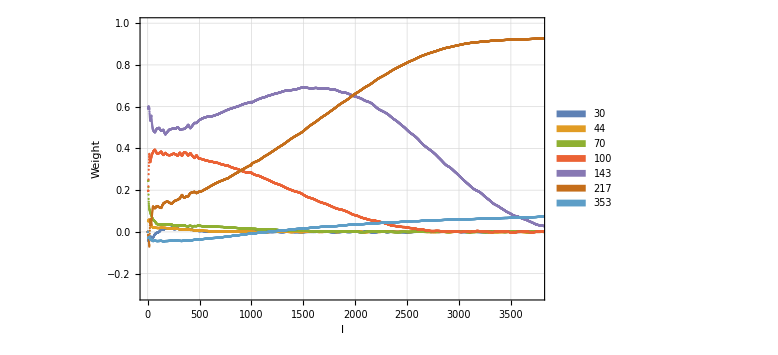

```mathematica
ListPlot[weightsFULL2018,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],PlotRange->{{1,3750},{-0.3,1}},ImageSize-> Large,FrameLabel->{"l","Weight",Style["SMICA FULL 2018",15]}]
```

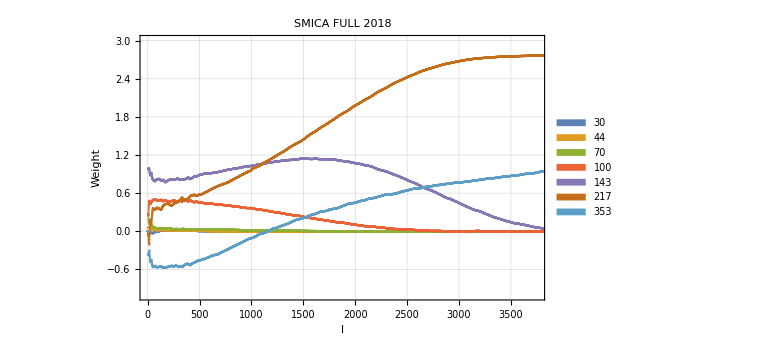

```mathematica
weightsFULLCMB2018plot=ListPlot[weightsFULLCMB2018,Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],PlotRange->{{1,3750},{-1,3}},ImageSize-> Large,FrameLabel->{Style["l",17],Style["Weight",17]},PlotLabel->Style["SMICA FULL 2018",17],FrameTicksStyle->Directive[Thick,12]]
```

```mathematica
Export["weightsFULLCMB_E_2018plot.pdf",weightsFULLCMB2018plot]
```

weightsFULLCMB_E_2018plot.pdf

#### SMICA 2018 Pipeline

```mathematica
beamtab=Table[Table[beamcorrection[[freq,l]],{freq,1,7}],{l,1,4001}];
```

```mathematica
P[l_]:=1
Subscript[Xnotcorr, Full][l_]:=(weightsFULL2018[[All,l]]/beamtab[[l]])/{0.98961854,0.99757886,0.99113965,1,1,1,1};
Xnotcorr[l_]:=Subscript[Xnotcorr, Full][l]
```

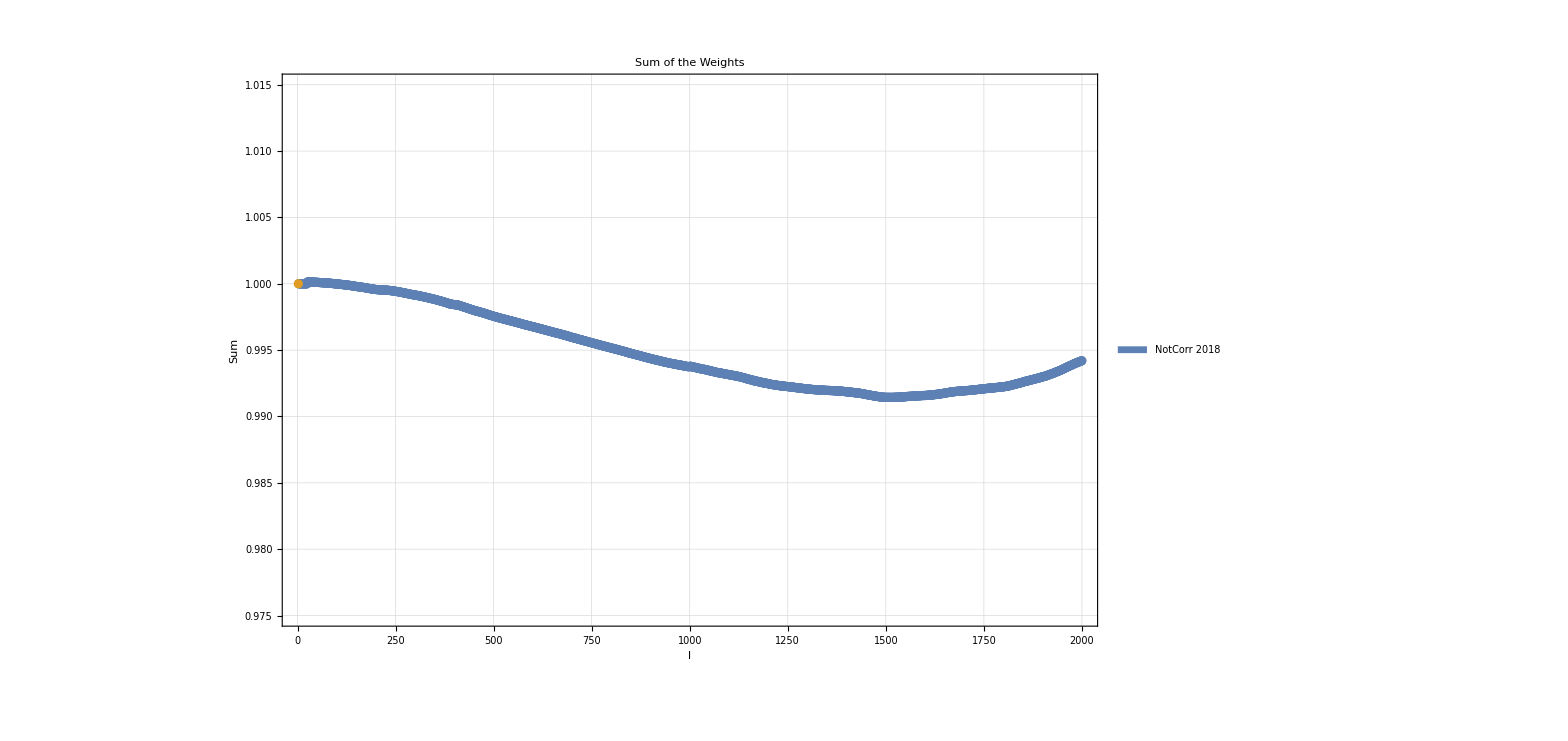

```mathematica
plot=ListPlot[{Table[Total[Xnotcorr[l]],{l,1,2000}],{l,1,2000}},GridLines->Automatic,PlotRange->{{1,2000},{0.975,1.015}},PlotLegends->Placed[SwatchLegend[{"NotCorr 2018"}],{Left,Bottom}],ImageSize->1200,Frame->True,PlotLabel->"Sum of the Weights",FrameLabel->{"l","Sum"}]
```

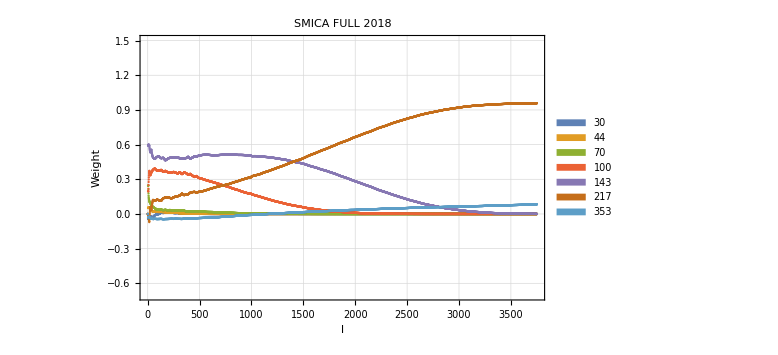

```mathematica
weightsFULLCMB2018plot=ListPlot[Table[Table[Xnotcorr[l+1],{l,0,3750}][[All,n]],{n,1,7}],PlotRange->{{1,3750},{-0.7,1.5}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[freqs],ImageSize-> Large,FrameLabel->{Style["l",17],Style["Weight",17]},PlotLabel->Style["SMICA FULL 2018",17],FrameTicksStyle->Directive[Thick,12]]
```

```mathematica
Export["weightsFULLCMB2018plot.pdf",weightsFULLCMB2018plot]
```

weightsFULLCMB2018plot.pdf

#### Effective Boost factor

```mathematica
SmicaBoostFactor2018[l_]:=Total[(Xnotcorr[l]*boostfactors)]
```

```mathematica
smicatable=Table[SmicaBoostFactor2018[l],{l,10,2000}];
```

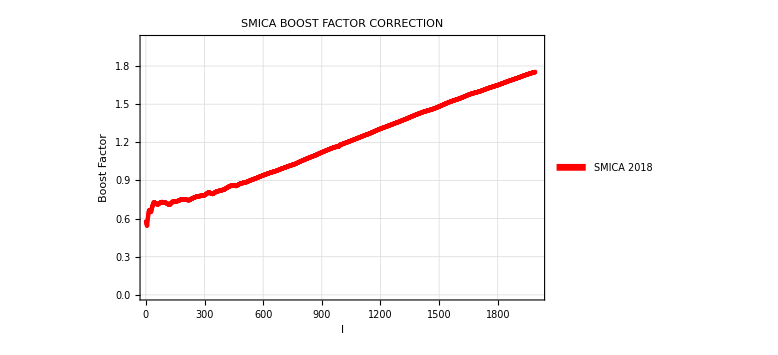

```mathematica
ListPlot[{smicatable},PlotRange->{{10,2000},{0,2}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018"}],PlotStyle->Red,ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

#### Binned Boost factor

```mathematica
binsize=200; nbins=10;
```

```mathematica
smicaboostfactorsbins=Table[Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}],{bin,1,nbins}]
```

{0.727066,0.787422,0.882902,0.993393,1.11653,1.23977,1.36217,1.47987,1.59401,1.70147}

```mathematica
smicaboostfactorsbinsforplot=Table[{bin*200-100,Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]
```

{{100,0.727066},{300,0.787422},{500,0.882902},{700,0.993393},{900,1.11653},{1100,1.23977},{1300,1.36217},{1500,1.47987},{1700,1.59401},{1900,1.70147}}

```mathematica
smicaboostfactorsBetaDeboostbins=smicaboostfactorsbins*βfid2018
```

{0.000896886,0.00097134,0.00108912,0.00122542,0.00137732,0.00152934,0.00168033,0.00182553,0.00196633,0.00209888}

```mathematica
smicaboostfactorsBetaDeboostbins*299792
```

{268.879,291.2,326.51,367.371,412.91,458.483,503.748,547.279,589.49,629.227}

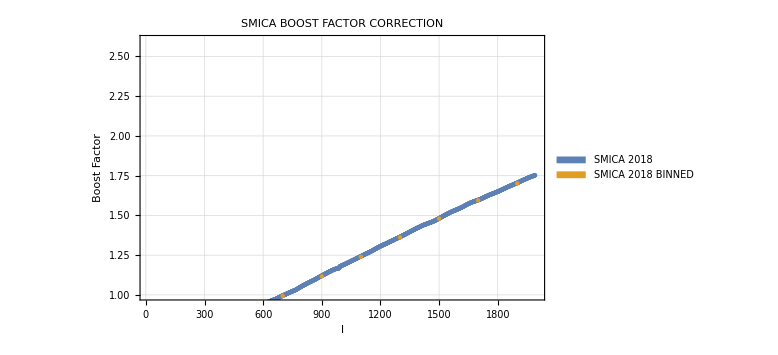

```mathematica
ListPlot[{smicatable,Table[{(binsize/2)+binsize*(bin-1),Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]},PlotRange->{{10,2000},{1,2.6}},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018","SMICA 2018 BINNED"}],ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

#### Binning Expected Error

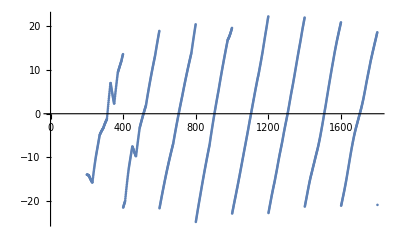

```mathematica
ListPlot[Table[{l,(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])*βfid2018*299792},{l,200,1800}]]
```

```mathematica
SmicaBinnedError=Total[Table[(2*l+1)(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]]),{l,200,1800}]*βfid2018*299792]/Total[Table[(2*l+1),{l,200,1800}]]
```

-0.235947

```mathematica
SmicaBinnedAbsError=Total[Table[(2*l+1)Abs[(SmicaBoostFactor2018[l]-smicaboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])],{l,200,1800}]*370]/Total[Table[(2*l+1),{l,200,1800}]]
```

10.5873

#### Mean Boost Factor and error

```mathematica
smicameanboostfactor=Sum[SmicaBoostFactor2018[l]*(2l+1),{l,1,2000}]/Sum[(2l+1),{l,1,2000}]
```

1.37458

```mathematica
smicameanboostfactor200to1800=Sum[SmicaBoostFactor2018[l]*(2l+1),{l,200,1800}]/Sum[(2l+1),{l,200,1800}]
```

1.30507

```mathematica
SmicaBinnedAbsError/(smicameanboostfactor200to1800*βfid2018*299792)
```

0.0219364

```mathematica
smicaboostfactorsBetaDeboostMean=-smicameanboostfactor*βfid2018
```

-0.00169564

## NILC weights

#### Needlets definitions

```mathematica
lpeakN={0,100,200,300,400,600,800,1000,1400,1800,2200,2800,3400};
lminN={1,0,100,200,300,400,600,800,1000,1400,1800,2200,2800};
lmaxN={100,200,300,400,600,800,1000,1400,1800,2200,2800,3400,4000};
needlet[band_,l_]:=Piecewise[{{0,l<lminN[[band]]},{Cos[((lpeakN[[band]]-l)/(lpeakN[[band]]-lminN[[band]]))*π/2],lminN[[band]]≤ l<lpeakN[[band]]},{1,l==lpeakN[[band]]},{Cos[((l-lpeakN[[band]])/(lmaxN[[band]]-lpeakN[[band]]))*π/2],lpeakN[[band]]<l≤ lmaxN[[band]]},{0,l>lmaxN[[band]]}}]
```

```mathematica
nilcneedletsplot=ListPlot[Table[needlet[band,l],{band,1,13},{l,1,2500}],PlotRange->{{0,2500},{0.01,1.05}},ImageSize->Large,Frame->True,FrameLabel->{Style["l",17],Style["Relative Weight",17]},PlotLabel->Style["NILC Needlets",17],PlotLegends->Placed[SwatchLegend[{"1-0","2-100","3-200","4-300","5-400","6-600","7-800","8-1000","9-1400","10-1800","11-2200","12-2800","13-3400"}],{Right,Bottom}],FrameTicksStyle->Directive[Black,15],Joined->True]
```

-Graphics-

```mathematica
Export["nilcneedletsplot.pdf",nilcneedletsplot]
```

nilcneedletsplot.pdf

#### Band Weights

```mathematica
bandweights[band_]:=Import["esky_dx11_mean_weight.fits","Data"][[1]][[band]]
```

```mathematica
bandweights[1]
```

{-0.0209161,0.0201601,0.128629,0.112945,0.671892,0.136561,-0.0492711}

```mathematica
bandweightsforplot[band_]:=bandweights[band]
```

```mathematica
colors={(*RGBColor[N[Normalize[{56,0,71}]]]*)Black,RGBColor[N[Normalize[{61,0,162}]]],RGBColor[N[Normalize[{13,0,255}]]],RGBColor[N[Normalize[{9,59,255}]]],RGBColor[N[Normalize[{25,174,255}]]],RGBColor[N[Normalize[{34,255,207}]]],RGBColor[N[Normalize[{35,255,96}]]],RGBColor[N[Normalize[{36,255,22}]]],RGBColor[N[Normalize[{86,255,13}]]],RGBColor[N[Normalize[{180,255,10}]]],RGBColor[N[Normalize[{254,211,11}]]],RGBColor[N[Normalize[{252,89,10}]]],RGBColor[N[Normalize[{251,19,29}]]]}
```

{GrayLevel[0],RGBColor[{0.35238928461181596, 0., 0.9358535099526916}],RGBColor[{0.05091427198434202, 0., 0.9987030273851704}],RGBColor[{0.034365416027046736, 0.22528439395508418, 0.9736867874329909}],RGBColor[{0.08071826920974581, 0.5617991536998309, 0.8233263459394073}],RGBColor[{0.10296886152666716, 0.7722664614500035, 0.6268986569417677}],RGBColor[{0.12740673275735537, 0.9282490529464463, 0.34945846699160327}],RGBColor[{0.13928296926770817, 0.9865876989795995, 0.08511737010804388}],RGBColor[{0.3191979202657341, 0.946458949625142, 0.04825084841226214}],RGBColor[{0.5763874626060793, 0.8165489053586124, 0.03202152570033774}],RGBColor[{0.7687868243279092, 0.6386378737527121, 0.03329391758900395}],RGBColor[{0.9422618492330557, 0.33278295468945224, 0.037391343223533956}],RGBColor[{0.9905948381758088, 0.07498526663482218, 0.11445119644262333}]}

#### Band weights plot

```mathematica
bandsWplot1=ListLogLinearPlot[Table[{freqs[[freq]],bandweightsforplot[band][[freq]]},{band,1,13},{freq,1,7}],PlotRange->{{25,450},{-0.1,1.2}},(*PlotStyle->Table[{colors[[n]],PointSize[0.02]},{n,1,13}],*)Frame->True,FrameLabel->{Style["Frequency (Ghz)",17],Style["Mean Weight",17]},PlotLabel->Style["Band Weights",17],FrameTicksStyle->Directive[Black,15]];
```

```mathematica
bandsWplot2=ListLogLinearPlot[Table[{freqs[[freq]],bandweightsforplot[band][[freq]]},{band,1,13},{freq,1,7}],Joined->True,PlotRange->{{25,450},{-0.1,1.2}},(*PlotStyle->Table[{colors[[n]]},{n,1,13}],*)PlotLegends->Placed[SwatchLegend[{"1","2","3","4","5","6","7","8","9","10","11","12","13"},LegendLabel->"Band (Needlet)"],{Left,Top}],Frame->True,FrameLabel->{Style["Frequency (Ghz)",17],Style["Mean Weight",17]},PlotLabel->Style["Band Weights",17],FrameTicksStyle->Directive[Black,15]];
```

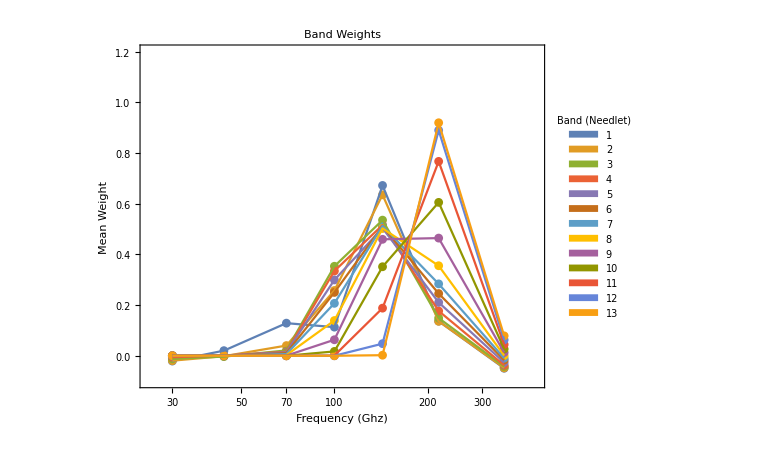

```mathematica
nilcbandsplot=Show[bandsWplot1,bandsWplot2,ImageSize-> Large,AspectRatio-> 0.8]
```

```mathematica
Export["nilcbandsplot_E.pdf",nilcbandsplot]
```

nilcbandsplot_E.pdf

#### Effective Boost Factor

```mathematica
needletWeights[band_,l_]:=bandweights[band]*needlet[band,l]
```

```mathematica
NILCweights=ParallelTable[(Total[Table[needletWeights[band,l],{band,1,13}]]/Total[Table[needlet[band,l],{band,1,13}]]),{l,1,2500}];
```

```mathematica
needlet[1,599]
```

0

```mathematica
NILCweights
```

{{-0.0208914,0.0198228,0.127261,0.11518,0.671322,0.136553,-0.0492475},2498,{0.,0.,0.,0.000448907,0.117806,0.828206,0.0535395}}
 |  |  |  |

```mathematica
NILCboostfactors2018[l_]:=Total[NILCweights[[l]]*boostfactors]
```

```mathematica
nilcboostable=Table[NILCboostfactors2018[l],{l,1,2500}];
```

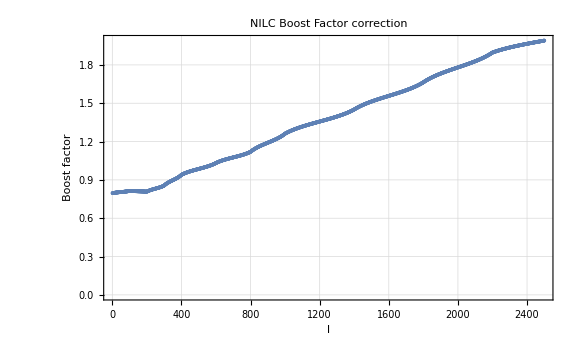

```mathematica
ListPlot[nilcboostable,GridLines->Automatic,Frame->True,PlotLabel->Style["NILC Boost Factor correction",15],FrameLabel->{"l","Boost factor"},ImageSize->Large]
```

#### Binned Boost factor

```mathematica
binsize=200; nbins=10;
```

```mathematica
nilcboostfactorsbins=Table[Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}],{bin,1,nbins}]
```

{0.809718,0.872262,0.988898,1.07821,1.19386,1.31664,1.39986,1.51205,1.60569,1.73015}

```mathematica
nilcboostfactorsbinsforplot=Table[{bin*binsize-100,Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]
```

{{100,0.809718},{300,0.872262},{500,0.988898},{700,1.07821},{900,1.19386},{1100,1.31664},{1300,1.39986},{1500,1.51205},{1700,1.60569},{1900,1.73015}}

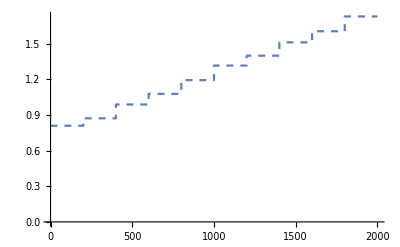

```mathematica
ListStepPlot[nilcboostfactorsbinsforplot,Center,PlotStyle->Dashed]
```

```mathematica
nilcboostfactorsBetaDeboostbins=nilcboostfactorsbins*βfid2018
```

{0.000998844,0.001076,0.00121987,0.00133004,0.00147271,0.00162417,0.00172683,0.00186521,0.00198074,0.00213426}

```mathematica
nilcboostfactorsBetaDeboostbins*299792
```

{299.445,322.575,365.709,398.736,441.508,486.913,517.69,559.176,593.809,639.833}

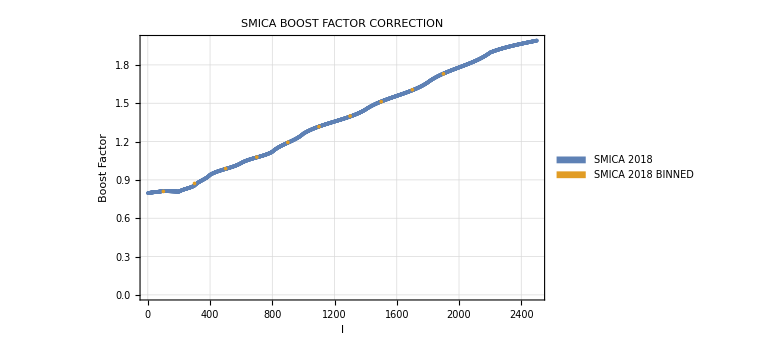

```mathematica
ListPlot[{nilcboostable,Table[{(binsize/2)+binsize*(bin-1),Sum[NILCboostfactors2018[l]*(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]/Sum[(2l+1),{l,1+((bin-1)*binsize),bin*binsize}]},{bin,1,nbins}]},Frame->True,GridLines->Automatic,PlotLegends->SwatchLegend[{"SMICA 2018","SMICA 2018 BINNED"}],ImageSize->Large,FrameLabel->{"l","Boost Factor"},PlotLabel->Style["SMICA BOOST FACTOR CORRECTION",15]]
```

```mathematica
ListPlot[Total[NILCweights,{2}],Frame->True]
```

-Graphics-

#### Binning Expected Error

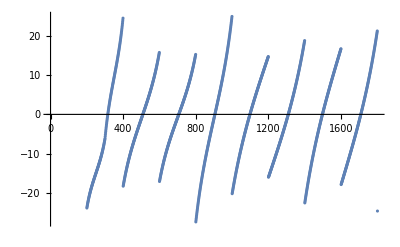

```mathematica
ListPlot[Table[{l,(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])*βfid2018*299792},{l,200,1800}]]
```

```mathematica
NilcBinnedError=Total[Table[(2*l+1)(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]]),{l,200,1800}]*βfid2018*299792]/Total[Table[(2*l+1),{l,200,1800}]]
```

-0.221554

```mathematica
NilcBinnedAbsError=Total[Table[(2*l+1)Abs[(NILCboostfactors2018[l]-nilcboostfactorsbinsforplot[[IntegerPart[10*l/2000+1],2]])],{l,200,1800}]*370]/Total[Table[(2*l+1),{l,200,1800}]]
```

9.16914

#### Mean Boost Factor and error

```mathematica
nilcmeanboostfactor=Sum[NILCboostfactors2018[l]*(2l+1),{l,1,2000}]/Sum[(2l+1),{l,1,2000}]
```

1.42178

```mathematica
nilcboostfactorsBetaDeboostMean=nilcmeanboostfactor*βfid2018
```

0.00175386

```mathematica
nilcmeanboostfactor200to1800=Sum[NILCboostfactors2018[l]*(2l+1),{l,200,1800}]/Sum[(2l+1),{l,200,1800}]
```

1.35622

```mathematica
NilcBinnedAbsError/(nilcmeanboostfactor200to1800*βfid2018*299792)
```

0.0182816

# Comparision plot EB

### Preamble

```mathematica
ckmsNU=299792;
rescaled[ddfactor_]:=IntegerPart[ddfactor*βfid2018*ckmsNU];
newaxis=Table[{rescaled[ddfactor],ddfactor},{ddfactor,0.3,2,0.1}]
```

{{110,0.3},{147,0.4},{184,0.5},{221,0.6},{258,0.7},{295,0.8},{332,0.9},{369,1.},{406,1.1},{443,1.2},{480,1.3},{517,1.4},{554,1.5},{591,1.6},{628,1.7},{665,1.8},{702,1.9},{739,2.}}

```mathematica
(*boostfactorplot=ListPlot[{smicatable,nilcboostable},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{{Style["Dipole Distortion Factor",17],Style["Effective Doppler Modulation (km/s)",17]},{Style["l",17],Style["Dipole Distortion Comparision",17]}},PlotStyle->{Red,Blue},PlotLegends->Placed[SwatchLegend[{Style[#,17]&@"SMICA",Style[#,17]&@"NILC"}],{Right,Bottom}],PlotRange->{{0,2000},{0.65,1.75}},ImageSize->Large,FrameTicks->{{Automatic,Table[{l,rescaled[l]},{l,0.6,1.8,0.2}]},{Automatic,None}},FrameTicksStyle->Directive[Thick,12],Joined->True]*)
```

```mathematica
(*Export["boostfactorplot.pdf",boostfactorplot]*)
```

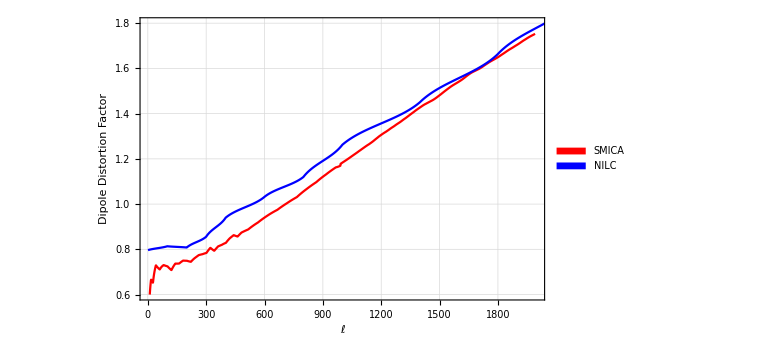

```mathematica
boostfactorplot=ListPlot[{smicatable,nilcboostable},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{{Style["Dipole Distortion Factor",28],Style["Effective Doppler Mod. (km/s)",28]},{Style[ToExpression["$\ell$",TeXForm,HoldForm],Large],""}},PlotLegends->Placed[SwatchLegend[{Style[#,28]&@"SMICA",Style[#,28]&@"NILC"},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMarkerSize->22],{Right,Bottom}],PlotStyle->{Red,Blue},PlotRange->{{0,2000},{0.6,1.8}},ImageSize->Large,FrameTicks->{{Automatic,Table[{l,rescaled[l]},{l,0.8,1.6,0.2}]},{Automatic,None}},FrameTicksStyle->Directive[Thick,25],PlotStyle->{{Blue,Thick},{Orange,Thick}},Joined->True]
```

```mathematica
nilcboostfactorsbinsforplot
```

{{100,0.809718},{300,0.872262},{500,0.988898},{700,1.07821},{900,1.19386},{1100,1.31664},{1300,1.39986},{1500,1.51205},{1700,1.60569},{1900,1.73015}}

```mathematica
nilcboostfactorsbinsforplot[[2-1;;2+1]]
```

{{100,0.809718},{300,0.872262},{500,0.988898}}

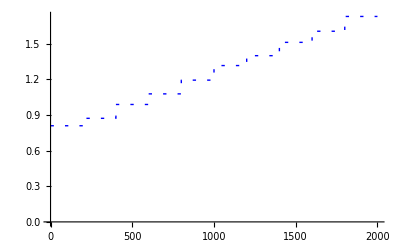

```mathematica
binnedplotnilc=ListStepPlot[nilcboostfactorsbinsforplot,Center,PlotStyle->Directive[Blue,Dashing[{0.006,0.02}],Thick],Joined->True]
```

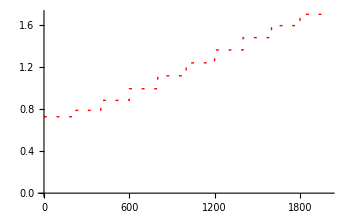

```mathematica
binnedplotsmica=ListStepPlot[smicaboostfactorsbinsforplot,Center,PlotStyle->Directive[Red,Dashing[{0.006,0.02}],Thick],Joined->True]
```

```mathematica
fiducialvec={-8.555645802435248688*10^(-5),-8.168953560588395214*10^(-4),9.203570039065433941*10^(-4)}
```

{-0.0000855564580243524869,-0.000816895356058839521,0.000920357003906543394}

```mathematica
normalizedfiducialvec=Normalize[fiducialvec]
```

{-0.0693567920947757188,-0.662220511246900856,0.746092239521505352}

```mathematica
eesmicasimsmean=Import["eesimsbinsmean_smica.dat"][[All,1]];
eenilcsimsmean=Import["eesimsbinsmean_nilc.dat"][[All,1]];
```

```mathematica
smicabetameanvecnorm=eesmicasimsmean;
nilcbetameanvecnorm=eenilcsimsmean;
```

```mathematica
expectederrorbybin=Import["doppler_EE_error_by_bin200size.dat","Table"][[All,1]]/(βfid2018);
```

```mathematica
nilcbetameannorm=Table[{117+200*(bin-1),Around[Norm[(nilcbetameanvecnorm[[bin]])]/(βfid2018),(expectederrorbybin[[bin]]/Sqrt[512])]},{bin,1,10}];
smicabetameannorm=Table[{83+200*(bin-1),Around[Norm[(smicabetameanvecnorm[[bin]])]/(βfid2018),((expectederrorbybin[[bin]]/Sqrt[512]))]},{bin,1,10}];
```

```mathematica
nilcbetameannorm
```

{{117,0.600.22},{317,0.780.13},{517,0.950.10},{717,1.090.08},{917,1.150.07},{1117,1.270.07},{1317,1.450.06},{1517,1.540.06},{1717,1.620.05},{1917,1.770.05}}

```mathematica
smicabetameannorm
```

{{83,0.510.22},{283,0.690.13},{483,0.840.10},{683,1.000.08},{883,1.080.07},{1083,1.190.07},{1283,1.410.06},{1483,1.510.06},{1683,1.610.05},{1883,1.740.05}}

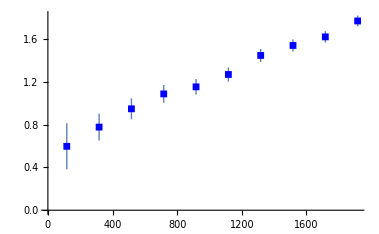

```mathematica
nilcbetameansimsplot=ListPlot[nilcbetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Blue,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

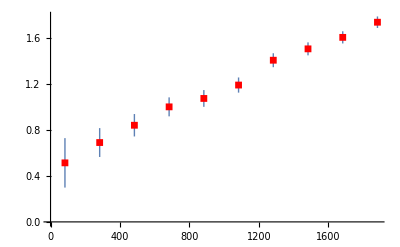

```mathematica
smicabetameansimsplot=ListPlot[smicabetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Red,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

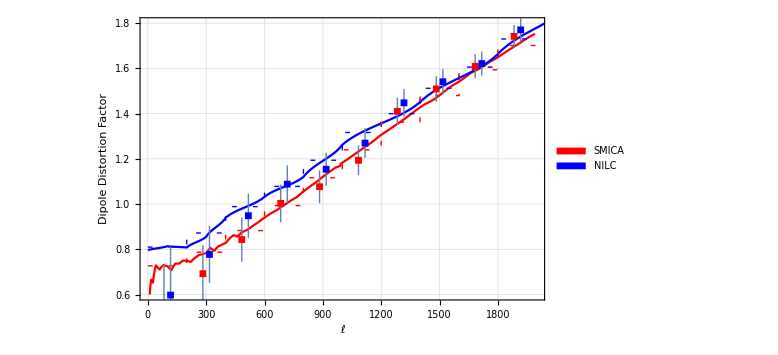

```mathematica
boostfactorplot=Show[boostfactorplot,binnedplotnilc,binnedplotsmica,smicabetameansimsplot,nilcbetameansimsplot]
```

```mathematica
Export["dipole_doppler_joined_plot_E_1024.pdf",boostfactorplot]
```

dipole_doppler_joined_plot_E_1024.pdf

```mathematica
nilcbetameannorm=Table[{117+200*(bin-1),Around[Norm[(nilcbetameanvecnorm[[bin]])]/(βfid2018),(expectederrorbybin[[bin]]/Sqrt[512])]},{bin,1,10}];
smicabetameannorm=Table[{83+200*(bin-1),Around[Norm[(smicabetameanvecnorm[[bin]])]/(βfid2018),((expectederrorbybin[[bin]]/Sqrt[512]))]},{bin,1,10}];
```

```mathematica
nilcbetameannorm
```

{{117,0.600.22},{317,0.780.13},{517,0.950.10},{717,1.090.08},{917,1.150.07},{1117,1.270.07},{1317,1.450.06},{1517,1.540.06},{1717,1.620.05},{1917,1.770.05}}

```mathematica
smicabetameannorm
```

{{83,0.510.22},{283,0.690.13},{483,0.840.10},{683,1.000.08},{883,1.080.07},{1083,1.190.07},{1283,1.410.06},{1483,1.510.06},{1683,1.610.05},{1883,1.740.05}}

```mathematica
nilcbetameansimsplot2=ListPlot[nilcbetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Blue,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

-Graphics-

```mathematica
smicabetameansimsplot2=ListPlot[smicabetameannorm,FrameTicksStyle->Directive[Thick,12],PlotStyle->{Red,Thick},PlotMarkers->{Graphics[{Rectangle[]},ImageSize->7]}]
```

-Graphics-

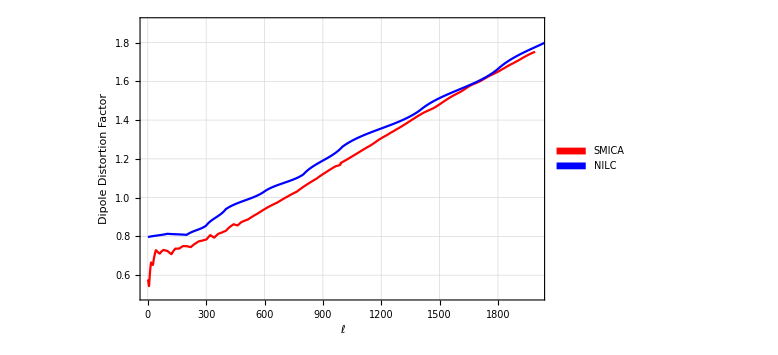

```mathematica
boostfactorplot2=ListPlot[{smicatable,nilcboostable},ImageSize->Large,Frame->True,GridLines->Automatic,FrameLabel->{{Style["Dipole Distortion Factor",28],Style["Effective Doppler Mod. (km/s)",28]},{Style[ToExpression["$\ell$",TeXForm,HoldForm],Large],""}},PlotLegends->Placed[SwatchLegend[{Style[#,28]&@"SMICA",Style[#,28]&@"NILC"},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMarkerSize->22],{Right,Bottom}],PlotStyle->{Red,Blue},PlotRange->{{0,2000},{0.5,1.9}},ImageSize->Large,FrameTicks->{{Automatic,Table[{l,rescaled[l]},{l,0.6,1.8,0.2}]},{Automatic,None}},FrameTicksStyle->Directive[Thick,25],PlotStyle->{{Blue,Thick},{Orange,Thick}},Joined->True]
```

```mathematica
nilcboostfactorsbinsforplot
```

{{100,0.809718},{300,0.872262},{500,0.988898},{700,1.07821},{900,1.19386},{1100,1.31664},{1300,1.39986},{1500,1.51205},{1700,1.60569},{1900,1.73015}}

```mathematica
nilcboostfactorsbinsforplot[[2-1;;2+1]]
```

{{100,0.809718},{300,0.872262},{500,0.988898}}

```mathematica
binnedplotnilc2=ListStepPlot[nilcboostfactorsbinsforplot,Center,PlotStyle->Directive[Blue,Dashing[{0.006,0.02}],Thick],Joined->True]
```

-Graphics-

```mathematica
binnedplotsmica2=ListStepPlot[smicaboostfactorsbinsforplot,Center,PlotStyle->Directive[Red,Dashing[{0.006,0.02}],Thick],Joined->True]
```

-Graphics-

### Final Plot

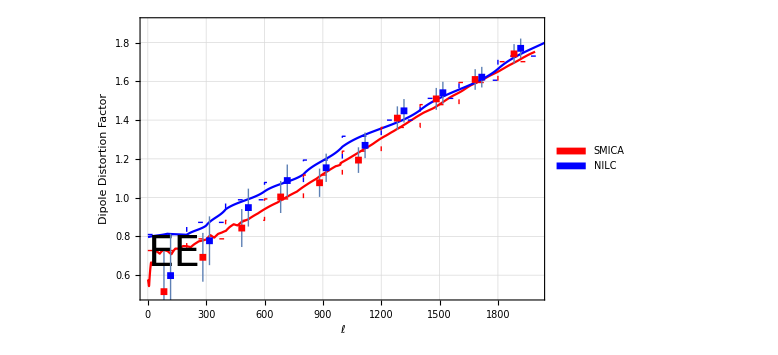

```mathematica
(*insettitleEE=Graphics[Text[Style["EE",42],{0.5,0.6},{-2.6,-12.15}]];*)
insettitleEE=Graphics[Text[Style["EE",42],{0.5,0.6},{-2.8,-12.95}]];
boostfactorplotEE=Show[{boostfactorplot2,binnedplotnilc2,binnedplotsmica2,smicabetameansimsplot2,nilcbetameansimsplot2,insettitleEE}]
```

```mathematica
Export["dipole_doppler_joined_plot_EE_1024_2.pdf",boostfactorplotEE,ImageSize->800]
```

dipole_doppler_joined_plot_EE_1024_2.pdf

```mathematica
Export["dipole_doppler_joined_plot_TT_1024_2.pdf",boostfactorplotTT,ImageSize->800]
```

dipole_doppler_joined_plot_TT_1024_2.pdf

# Joined → EE+TT

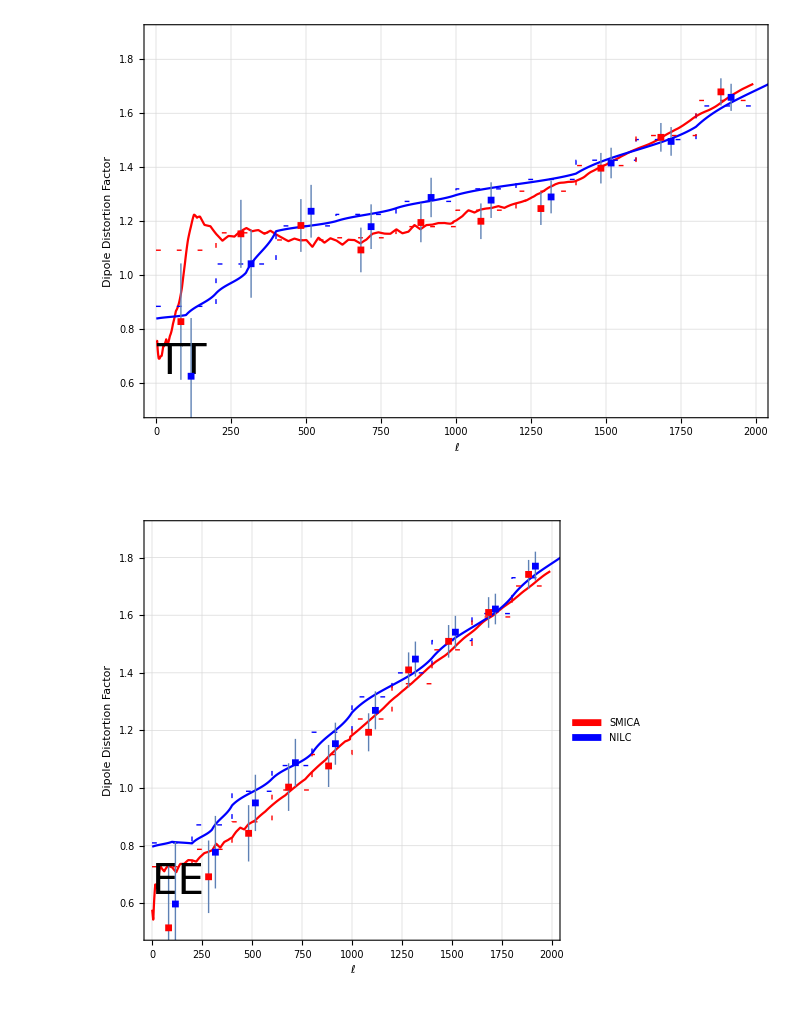

```mathematica
joinedTTEEplot=GraphicsColumn[{boostfactorplotTT,boostfactorplotEE},ImageSize->800,Spacings->0,ImagePadding->{{-15,-15},{240,240}}]
```

```mathematica
Export["joinedTTEEplot.pdf",joinedTTEEplot]
```

joinedTTEEplot.pdf